# Paper Figures – Energies (F1-F3)

Figures drawable from the energy campaign alone: level diagrams (F1), the transition scheme at the base geometry (F2), and the geometry trends (F3), including the eta fine structure of XX0101. The optics figures (F4-F7: oscillator strengths, chi3, absorption) live in a separate notebook once the dipole derivation lands. All plots are Missing-tolerant: partial campaign data simply produces fewer points. Energies in meV (confinement scale; the gap enters only where absolute scales are labeled). Exports go to this notebook's folder as PDF.

## Load definitions and results

```mathematica
dir = NotebookDirectory[];
Get[FileNameJoin[{ParentDirectory[dir, 3], "shared", "numerics", "definitions.wl"}]];
prodFile = FileNameJoin[{ParentDirectory[dir], "01-numerics", "production-results.wxf"}];
prodResults = Import[prodFile, "WXF"];
Length[prodResults]
```

38

```mathematica
(* identical key construction as Production-Runs.nb *)
prodKey[label_, aa_, cc_] :=
  StringJoin[label, "|a=", ToString[aa], "|c=", ToString[cc]];
nmToRB = 10.^-9/rB;
geomNm = {{50, 6}, {50, 7}, {50, 8}, {50, 10}, {40, 6}, {60, 6}};
geometries = nmToRB geomNm;
legacy = {{5.0, 0.5}, {5.0, 0.55}};   (* rB-defined extra points, a ~ 50.5 nm *)

(* total energy in meV; Missing if the run doesn't exist *)
val[label_, aa_, cc_] :=
  With[{r = Lookup[prodResults, prodKey[label, aa, cc]]},
   If[AssociationQ[r], ER2meV r["total"], Missing["NotRun"]]];
dif[x_, y_] := If[NumericQ[x] && NumericQ[y], x - y, Missing["NotRun"]];

(* which runs exist -- quick orientation *)
Keys[prodResults] // Sort // Column
```

X00|a=4.94577|c=0.593492
X00|a=4.94577|c=0.692407
X00|a=4.94577|c=0.791323
X00|a=5.|c=0.5
X00|a=5.|c=0.55
X01|a=4.94577|c=0.593492
X01|a=4.94577|c=0.692407
X01|a=4.94577|c=0.791323
X01|a=5.|c=0.5
X01|a=5.|c=0.55
X10|a=4.94577|c=0.593492
X10|a=4.94577|c=0.692407
X10|a=4.94577|c=0.791323
X10|a=5.|c=0.5
X10|a=5.|c=0.55
X11|a=4.94577|c=0.593492
X11|a=4.94577|c=0.692407
X11|a=4.94577|c=0.791323
XX0000|a=4.94577|c=0.593492
XX0000|a=4.94577|c=0.692407
XX0000|a=4.94577|c=0.791323
XX0000|a=5.|c=0.5
XX0000|a=5.|c=0.55
XX0010|a=4.94577|c=0.593492
XX0010|a=5.|c=0.5
XX0010|a=5.|c=0.55
XX0101mm|a=4.94577|c=0.593492
XX0101mp|a=4.94577|c=0.593492
XX0101pm|a=4.94577|c=0.593492
XX0101pp|a=4.94577|c=0.593492
XX0101pp|a=4.94577|c=0.692407
XX0101pp|a=4.94577|c=0.791323
XX1000|a=4.94577|c=0.593492
XX1000|a=5.|c=0.5
XX1000|a=5.|c=0.55
XX1111|a=4.94577|c=0.593492
XX1111|a=4.94577|c=0.692407
XX1111|a=4.94577|c=0.791323

## F1: level diagrams (correlated energies)

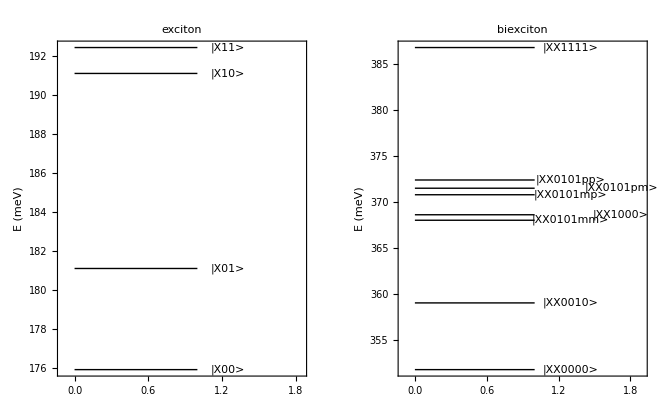

```mathematica
(* staggered-label level column, as in the preview notebook *)
labelX[vals_, x0_, dx_, tol_] :=
  Module[{prev = -Infinity, tog = 0},
   Table[
    If[vals[[n]] - prev < tol, tog = 1 - tog, tog = 0];
    prev = vals[[n]]; x0 + tog dx, {n, Length[vals]}]];

levelColumn[levels_, title_, x0_] :=
  Module[{vals = levels[[All, 1]], xs, tol},
   tol = 0.045 (Max[vals] - Min[vals] + $MachineEpsilon);
   xs = labelX[vals, x0, 0.42, tol];
   Graphics[{
     Table[{Thick, Line[{{0, vals[[n]]}, {1, vals[[n]]}}],
       Text[Style[levels[[n, 2]], 11], {xs[[n]], vals[[n]]}]},
      {n, Length[levels]}]},
    Frame -> {{True, False}, {False, False}},
    FrameLabel -> {None, "E (meV)"}, PlotLabel -> title,
    PlotRange -> {{-0.1, x0 + 0.6}, All}, AspectRatio -> 1.4]];

xLabels = {"X00", "X01", "X10", "X11"};
xxLabels = {"XX0000", "XX0010", "XX1000", "XX0101pp", "XX0101pm",
   "XX0101mp", "XX0101mm", "XX1111"};

levelData[labels_, aa_, cc_] := Sort@Select[
    {val[#, aa, cc], "|" <> # <> ">"} & /@ labels,
    NumericQ[First[#]] &];

figLevels[aa_, cc_, titleNm_] :=
  GraphicsRow[{
    levelColumn[levelData[xLabels, aa, cc], "exciton", 1.25],
    levelColumn[levelData[xxLabels, aa, cc], "biexciton", 1.3]},
   PlotLabel -> Style["Correlated energy levels   " <> titleNm, Bold, 14],
   ImageSize -> 660];

figF1base = figLevels[Sequence @@ geometries[[1]], "(a=50 nm, c=6 nm)"]
```

```mathematica
figF1thick = figLevels[Sequence @@ geometries[[4]], "(a=50 nm, c=10 nm)"]
```

## F2: transition scheme at the base geometry

```mathematica
(* the diamond + binding + eta splittings, base geometry, meV *)
Module[{aa = geometries[[1, 1]], cc = geometries[[1, 2]],
  x00, x11, b0, bpp, b11},
 x00 = val["X00", aa, cc]; x11 = val["X11", aa, cc];
 b0 = val["XX0000", aa, cc]; bpp = val["XX0101pp", aa, cc];
 b11 = val["XX1111", aa, cc];
 figF2 = Dataset[{
    <|"quantity" -> "E(X00)", "meV" -> x00|>,
    <|"quantity" -> "E(X11)", "meV" -> x11|>,
    <|"quantity" -> "E(XX0000)", "meV" -> b0|>,
    <|"quantity" -> "E(XX0101pp)", "meV" -> bpp|>,
    <|"quantity" -> "E(XX1111)", "meV" -> b11|>,
    <|"quantity" -> "Ebind(XX0000) = 2E(X00)-E(XX0000)",
     "meV" -> dif[2 x00, b0]|>,
    <|"quantity" -> "T(XX0000->X00)", "meV" -> dif[b0, x00]|>,
    <|"quantity" -> "T(XX0101->X00)", "meV" -> dif[bpp, x00]|>,
    <|"quantity" -> "T(XX0101->X11)", "meV" -> dif[bpp, x11]|>,
    <|"quantity" -> "T(XX1111->X11)", "meV" -> dif[b11, x11]|>,
    <|"quantity" -> "J(etaH): E(pm)-E(pp)",
     "meV" -> dif[val["XX0101pm", aa, cc], bpp]|>,
    <|"quantity" -> "J(etaE): E(mp)-E(pp)",
     "meV" -> dif[val["XX0101mp", aa, cc], bpp]|>,
    <|"quantity" -> "E(mm)-E(pp)",
     "meV" -> dif[val["XX0101mm", aa, cc], bpp]|>}]]
```

## F3: geometry trends

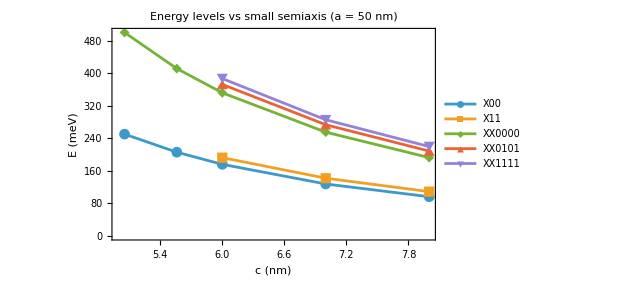

```mathematica
(* c-scan at a ~ 50 nm: new grid (a = 50 nm exactly) + legacy points
   (a = 50.5 nm, plotted as open markers). x-axis in nm. *)
cScanGeoms = Join[
   Select[geometries, Abs[#[[1]] - geometries[[1, 1]]] < 10^-6 &],
   legacy];
cNm[g_] := g[[2]] rB 10^9;

trendData[label_] := Sort@Select[
    {cNm[#], val[label, #[[1]], #[[2]]]} & /@ cScanGeoms,
    NumericQ[Last[#]] &];

trendPlot[labels_, plotLabel_, legend_] :=
  ListLinePlot[trendData /@ labels,
   PlotMarkers -> Automatic, Frame -> True,
   FrameLabel -> {"c (nm)", "E (meV)"},
   PlotLegends -> legend, PlotLabel -> plotLabel, ImageSize -> 460];

figF3levels = trendPlot[{"X00", "X11", "XX0000", "XX0101pp",
   "XX1111"}, "Energy levels vs small semiaxis (a = 50 nm)",
  {"X00", "X11", "XX0000", "XX0101", "XX1111"}]
```

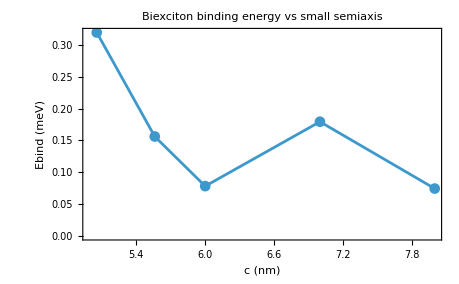

```mathematica
(* binding energy and diamond transition energies vs c *)
bindData = Sort@Select[
    Module[{aa = #[[1]], cc = #[[2]]},
      {cNm[#], dif[2 val["X00", aa, cc], val["XX0000", aa, cc]]}] & /@
     cScanGeoms, NumericQ[Last[#]] &];
figF3bind = ListLinePlot[bindData, PlotMarkers -> Automatic, Frame -> True,
  FrameLabel -> {"c (nm)", "Ebind (meV)"},
  PlotLabel -> "Biexciton binding energy vs small semiaxis",
  ImageSize -> 460]
```

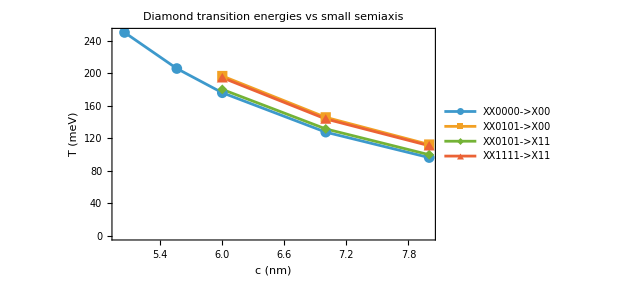

```mathematica
transData[l1_, l2_] := Sort@Select[
    Module[{aa = #[[1]], cc = #[[2]]},
      {cNm[#], dif[val[l1, aa, cc], val[l2, aa, cc]]}] & /@ cScanGeoms,
    NumericQ[Last[#]] &];
figF3trans = ListLinePlot[
  {transData["XX0000", "X00"], transData["XX0101pp", "X00"],
   transData["XX0101pp", "X11"], transData["XX1111", "X11"]},
  PlotMarkers -> Automatic, Frame -> True,
  FrameLabel -> {"c (nm)", "T (meV)"},
  PlotLegends -> {"XX0000->X00", "XX0101->X00", "XX0101->X11",
    "XX1111->X11"},
  PlotLabel -> "Diamond transition energies vs small semiaxis",
  ImageSize -> 460]
```

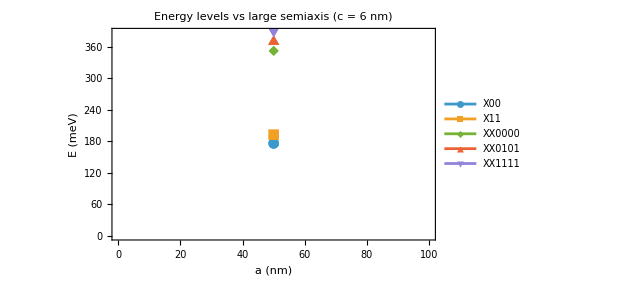

```mathematica
(* a-scan at c = 6 nm *)
aScanGeoms = Select[geometries, Abs[#[[2]] - geometries[[1, 2]]] < 10^-6 &];
aNm[g_] := g[[1]] rB 10^9;
aData[label_] := Sort@Select[
    {aNm[#], val[label, #[[1]], #[[2]]]} & /@ aScanGeoms,
    NumericQ[Last[#]] &];
figF3aScan = ListLinePlot[aData /@ {"X00", "X11", "XX0000",
    "XX0101pp", "XX1111"},
  PlotMarkers -> Automatic, Frame -> True,
  FrameLabel -> {"a (nm)", "E (meV)"},
  PlotLegends -> {"X00", "X11", "XX0000", "XX0101", "XX1111"},
  PlotLabel -> "Energy levels vs large semiaxis (c = 6 nm)",
  ImageSize -> 460]
```

## Error bars and health

```mathematica
(* worst identity spread per run -- quote as the relative error bar *)
worstSpread[res_] := Max[Cases[res["check"],
    KeyValuePattern["relSpread" -> s_] :> s, {1}]];
Dataset[worstSpread /@ Select[prodResults, AssociationQ]]
```

## Export

```mathematica
Export[FileNameJoin[{dir, "F1-levels-base.pdf"}], figF1base];
(*Export[FileNameJoin[{dir, "F1-levels-thick.pdf"}], figF1thick];*)
Export[FileNameJoin[{dir, "F3-levels-cscan.pdf"}], figF3levels];
Export[FileNameJoin[{dir, "F3-binding.pdf"}], figF3bind];
Export[FileNameJoin[{dir, "F3-transitions.pdf"}], figF3trans];
(*Export[FileNameJoin[{dir, "F3-levels-ascan.pdf"}], figF3aScan];*)
FileNames["*.pdf", dir]
```

{C:\Users\davit\Documents\PhD\projects\biexciton\03-figures\F1-levels-base.pdf,C:\Users\davit\Documents\PhD\projects\biexciton\03-figures\F3-binding.pdf,C:\Users\davit\Documents\PhD\projects\biexciton\03-figures\F3-levels-cscan.pdf,C:\Users\davit\Documents\PhD\projects\biexciton\03-figures\F3-transitions.pdf}